```mathematica
ranges=Import["https://raw.githubusercontent.com/HALtheWise/POE-lab2/master/docs/zeroPassDistances.csv","Data"]
```

{{cm, voltage},{18,550},{20,529},{16,570},{14,583},{12,575},{25,472},{30,409},{40,314},{50,249},{60,207},{70,174},{80,148},{90,126},{100,119},{110,107},{120,94},{130,89},{140,80},{150,72},{}}

```mathematica
rangeVoltage=ranges[[2;;Length[ranges]-1]]
```

{{18,550},{20,529},{16,570},{14,583},{12,575},{25,472},{30,409},{40,314},{50,249},{60,207},{70,174},{80,148},{90,126},{100,119},{110,107},{120,94},{130,89},{140,80},{150,72}}

782.774-15.9408 x+0.128033 x^2-0.000356379 x^3

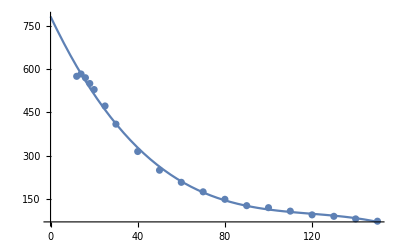

```mathematica
Fit[rangeVoltage,{1,x,x^2,x^3},x]
plot1=Plot[%,{x,0,150}];
plot2=ListPlot[rangeVoltage];
Show[plot1,plot2]
```